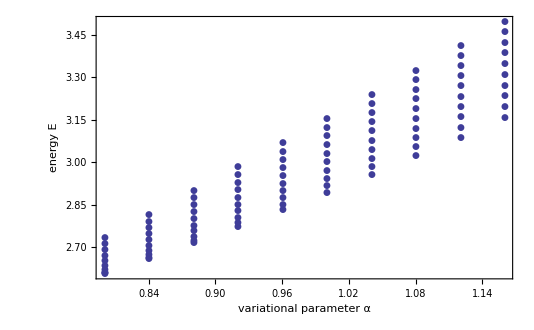

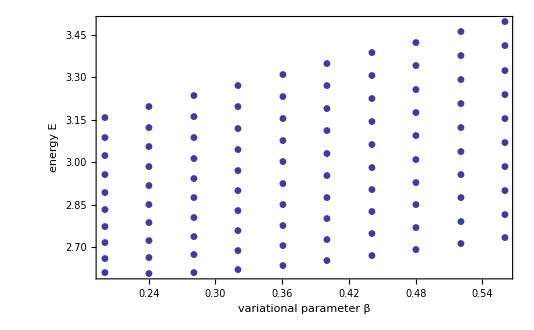

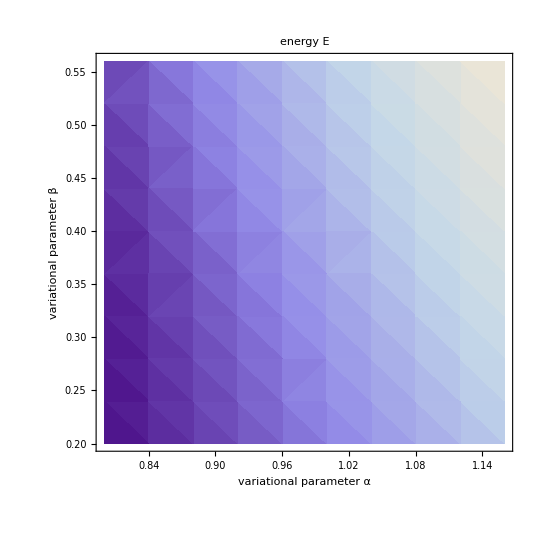

-Graphics3D-

{{2,1}}

{0.8,0.24,2.60595}

```mathematica
Needs["ErrorBarPlots`"];

(*f=Import["/Users/anjabielefeld/Documents/Studium/Oslo/UiO/CP/Project-3/build-MonteCarlo-G_49-Release/vmc.dat","Table"];*)

(*Importiere aus .dat*)
f = Import["/Users/anjabielefeld/Documents/Studium/Oslo/UiO/CP/vmci.dat","Table"];
(*Tabelle der Form {α, β, E}*)
flist=Table[{f[[i,1]],f[[i,2]],f[[i,3]]},{i,2,101}];
(*Tabelle der Form {E}*)
flistE =Table[{f[[i,3]]},{i,2,11}];
(*Erstelle Tabellen für ErrorListPlot mit Fehler für Energie*)
ferralpha=Table[{{f[[i,1]],f[[i,3]]},ErrorBar[0,{-f[[i,5]],f[[i,5]]}]},{i,2,101}];
ferrbeta=Table[{{f[[i,2]],f[[i,3]]},ErrorBar[0,{-f[[i,5]],f[[i,5]]}]},{i,2,101}];
(*Plots*)
ErrorListPlot[ferralpha,PlotLabel->Style["",FontSize ->23],LabelStyle->FontSize->23,PlotMarkers->Automatic,Frame->True,PlotRange->All,FrameLabel->{"variational parameter α","energy E"}]
ErrorListPlot[ferrbeta,PlotLabel->Style["",FontSize ->23],LabelStyle->FontSize->23,PlotMarkers->Automatic,Frame->True,PlotRange->All,FrameLabel->{"variational parameter β","energy E"}]
(* Ohne ErrorBarPlots-Package...
falpha=Table[{{f[[i,1]],f[[i,3]]}},{i,2,82}];
fbeta=Table[{{f[[i,2]],f[[i,3]]}},{i,2,82}];
ListPlot[falpha,PlotLabel->Style["",FontSize ->23],LabelStyle->FontSize->23,PlotMarkers->Automatic,Frame->True,PlotRange->All,FrameLabel->{"variational parameter α","energy E"}]
ListPlot[fbeta,PlotLabel->Style["",FontSize ->23],LabelStyle->FontSize->23,PlotMarkers->Automatic,Frame->True,PlotRange->All,FrameLabel->{"variational parameter β","energy E"}]*)

ListDensityPlot[flist,LabelStyle->FontSize->23,Frame->True,PlotLabel->Style["energy E",FontSize ->23],FrameLabel->{"variational parameter α","variational parameter β"}]
ListPlot3D[flist]


(*Finde Minimum von E*)
a =Position[flistE,Min[flistE]]
(*Gib {α,β,E} für das Minimum aus*)
pos = Part[flist,a[[1]][[1]]]
(*or pos = v[[a]]*)
```